Номер 2

(1+4 x^2+x^6)^(1/5) Sin[1/18+(2 x)/(√31)+(√(5+x))/7]

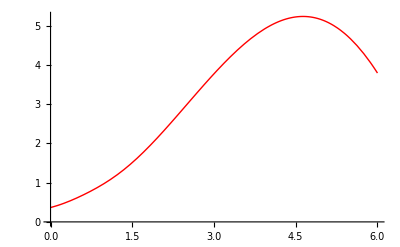

```mathematica
a =0;
b= 6;
n1 = 6;
n2 = 10;
f[x_]=(x^6+4 x^2+1)^(1/5)*Sin[(2*x/√31+1/7*√(x+5)+1/18)]
graph = Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}]
```

```mathematica
T1[i_]=Cos[(Pi (2 i+1))/(2*n1+2)];
```

```mathematica
T2[i_]=Cos[(Pi (2 i+1))/(2*n2+2)];
```

```mathematica
tabl1=Table[{x1=(a+b)/2+(b-a)/2*T1[i],f[x1]},{i,0,n1}]//N;
tabl2=Table[{x2=(a+b)/2+(b-a)/2*T2[i],f[x2]},{i,0,n2}]//N;
{TableForm[tabl1]}
{TableForm[tabl2]}
```

{5.92478 | 3.94979
5.34549 | 4.85644
4.30165 | 5.15814
3. | 3.77226
1.69835 | 1.76629
0.654506 | 0.723811
0.0752163 | 0.395238}

{5.96946 | 3.85642
5.7289 | 4.31931
5.26725 | 4.93631
4.62192 | 5.23197
3.8452 | 4.84025
3. | 3.77226
2.1548 | 2.43768
1.37808 | 1.36639
0.732751 | 0.77941
0.271104 | 0.487098
0.0305357 | 0.377634}

Номер 2(а):

```mathematica
diftabl1=Array[dif1,{n1+1,n1+1},{0,0}];
For[k=1,k≤n1,k++,For[i=n1,i≥n1-k,i--,dif1[i,k]=" "]];
For[i=0,i≤n1,i++,dif1[i,0]=tabl1[[i+1,2]]];
For[k=1,k≤n1,k++,For[i=0,i≤n1-k,i++,dif1[i,k]=(dif1[i+1,k-1]-dif1[i,k-1])/(tabl1[[i+1+k,1]]-tabl1[[i+1,1]])]];
PaddedForm[TableForm[diftabl1],{n1,n1-1}]
```

3.94979 | -1.56512 | -0.78619 | -0.07147 |  0.00866 |  0.00142 | -0.00058
 4.85644 | -0.28902 | -0.57716 | -0.10808 |  0.00117 |  0.00479 |  
 5.15814 |  1.06471 | -0.18299 | -0.11358 | -0.02408 |   |  
 3.77226 |  1.54110 |  0.23126 | -0.01182 |   |   |  
 1.76629 |  0.99869 |  0.26584 |   |   |   |  
 0.72381 |  0.56720 |   |   |   |   |  
 0.39524 |   |   |   |   |   |

```mathematica
diftabl2=Array[dif2,{n2+1,n2+1},{0,0}];
For[k=1,k≤n2,k++,For[i=n2,i≥n2-k,i--,dif2[i,k]=""]];
For[i=0,i≤n2,i++,dif2[i,0]=tabl2[[i+1,2]]];
For[k=1,k≤n2,k++,For[i=0,i≤n2-k,i++,dif2[i,k]=(dif2[i+1,k-1]-dif2[i,k-1])/(tabl2[[i+1+k,1]]-tabl2[[i+1,1]])]];
PaddedForm[TableForm[diftabl2],{n2,n2-1}]
```

3.856424940 | -1.924136399 | -0.836803906 | -0.032148915 |  0.014018289 |  0.001003497 | -0.000026583 | -0.000015235 | -0.000028304 | -2.966715484×10^-6 |  0.000014012
 4.319311238 | -1.336519640 | -0.793481896 | -0.061927499 |  0.011038440 |  0.001104901 |  0.000043365 |  0.000132987 | -0.000011399 | -0.000086183 | 
 4.936311872 | -0.458156182 | -0.676829171 | -0.092050252 |  0.007089419 |  0.000916228 | -0.000621059 |  0.000195201 |  0.000479704 |  | 
 5.231972092 |  0.504329454 | -0.468128354 | -0.114115689 |  0.003526053 |  0.003732418 | -0.001596309 | -0.002316870 |  |  | 
 4.840246907 |  1.263597341 | -0.186591242 | -0.125553659 | -0.010989958 |  0.010677669 |  0.009041339 |  |  |  | 
 3.772257378 |  1.579010307 |  0.123164716 | -0.091348005 | -0.049152945 | -0.023811985 |  |  |  |  | 
 2.437681545 |  1.379246688 |  0.330273364 |  0.042785270 |  0.021555896 |  |  |  |  |  | 
 1.366386461 |  0.909581104 |  0.249678822 | -0.003005201 |  |  |  |  |  |  | 
 0.779409880 |  0.633193256 |  0.253728456 |  |  |  |  |  |  |  | 
 0.487097946 |  0.455021175 |  |  |  |  |  |  |  |  | 
 0.377634258 |  |  |  |  |  |  |  |  |  |

Номер 2(б)

```mathematica
P1[x_]=1;P2[x_]=1;Pr1[x_]=dif1[0,0];Pr2[x_]=dif2[0,0];
For[i=0,i<n1,i++,P1[x_]=P1[x] (x-tabl1[[i+1,1]]);Pr1[x_]=Pr1[x]+dif1[0,i+1] P1[x]]
Pr1[x]//Simplify

For[i=0,i<n2,i++,P2[x_]=P2[x] (x-tabl2[[i+1,1]]);Pr2[x_]=Pr2[x]+dif2[0,i+1] P2[x]]
Pr2[x]//Simplify
```

0.352119+0.589375 x-0.243131 x^2+0.393646 x^3-0.11905 x^4+0.0134766 x^5-0.000576143 x^6

0.36874+0.263779 x+0.943757 x^2-1.47762 x^3+1.4824 x^4-0.807 x^5+0.262579 x^6-0.0533356 x^7+0.00664375 x^8-0.000464936 x^9+0.000014012 x^10

Изобразим полученные многочлены
n=6

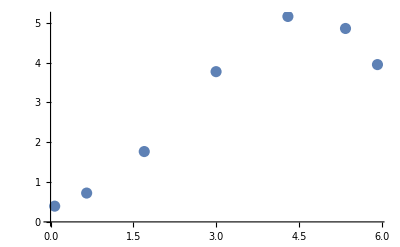

```mathematica
graph1D=ListPlot[tabl1,PlotStyle->{Darker,PointSize[0.02]}]
```

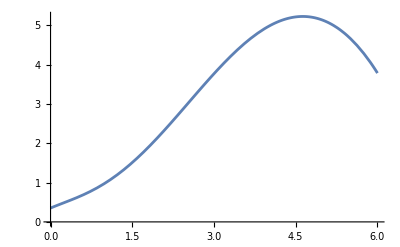

```mathematica
graph1Pr=Plot[Pr1[x],{x,a,b}]
```

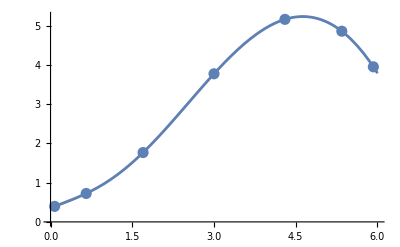

```mathematica
Show[graph,graph1D,graph1Pr]
```

Изобразим n=10

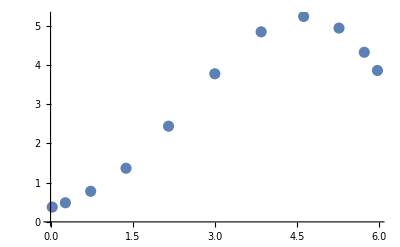

```mathematica
graph2D=ListPlot[tabl2,PlotStyle->{Darker,PointSize[0.02]}]
```

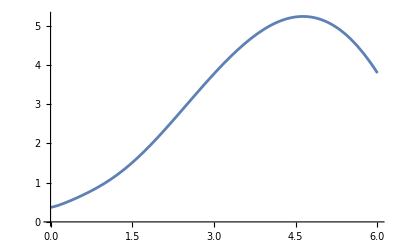

```mathematica
graph2Pr=Plot[Pr2[x],{x,a,b}]
```

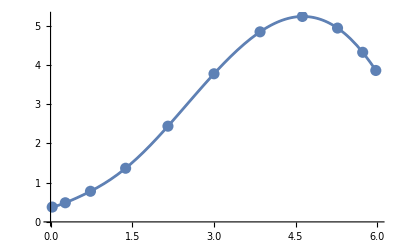

```mathematica
Show[graph,graph2D,graph2Pr]
```

Номер 2(в):

```mathematica
Intf1=Interpolation[tabl1]
```

InterpolatingFunction[…]

```mathematica
Intf2=Interpolation[tabl2]
```

InterpolatingFunction[…]

Изобразим полученные интерполирующие функции:

```mathematica
graph1Intf=Plot[Intf1[x],{x,a,b}];
```

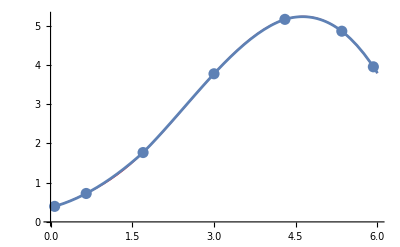

```mathematica
Show[graph,graph1D,graph1Intf]
```

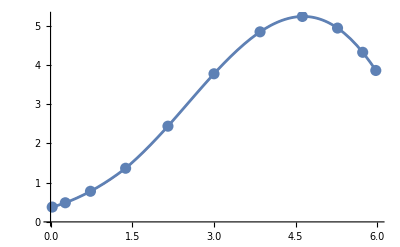

```mathematica
graph2Intf=Plot[Intf2[x],{x,a,b}];
Show[graph,graph2D,graph2Intf]
```

Номер 2(г):

```mathematica
x0= 2.4316;
Print["f[x]=",f[x0]]
Print["Pr1[x0]=",Pr1[x0],", Pr2[x0]=",Pr2[x0]]
Print["Intf1[x0]=",Intf1[x0],", Intf2[x0]=",Intf2[x0]]
```

f[x]=2.8766

Pr1[x0]=2.87181, Pr2[x0]=2.87698

Intf1[x0]=2.88404, Intf2[x0]=2.87618

Номер 2(д):

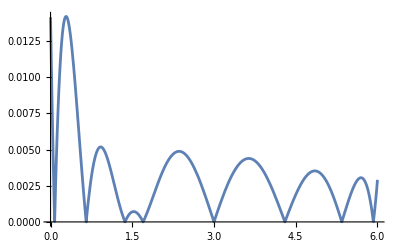

```mathematica
Rp1[x_]=Abs[f[x]-Pr1[x]]//Simplify;
graphErr1=Plot[Rp1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErr1=FindMaximum[{Rp1[x],0<=x<=6},x]
```

{0.00518282,{x→0.919784}}

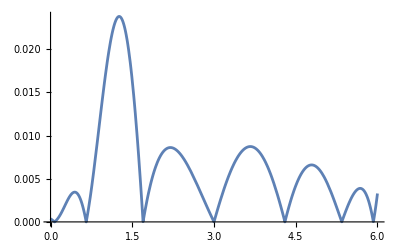

```mathematica
RI1[x_]=Abs[f[x]-Intf1[x]]//Simplify;
graphErrI1=Plot[RI1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrI1=FindMaximum[RI1[x],{x,3,4}]
```

{0.00873549,{x→3.66656}}

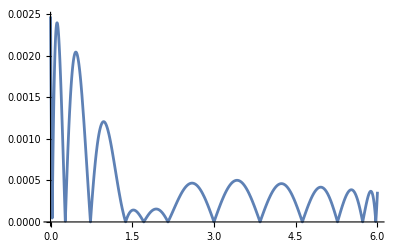

```mathematica
Rp2[x_]=Abs[f[x]-Pr2[x]]//Simplify;
graphErr2=Plot[Rp2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErr2=FindMaximum[Rp2[x],{x,0.1,0.6}]
```

{0.00239732,{x→0.119573}}

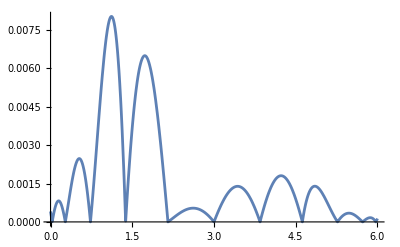

```mathematica
RI2[x_]=Abs[f[x]-Intf2[x]]//Simplify;
graphErrI2=Plot[RI2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrI2=FindMaximum[RI2[x],{x,3,4}]
```

{0.00139181,{x→3.4336}}

Номер 3

Для равностоящих :
1) maxErr1:
{0.0247999, {x → 0.261447}}
2)maxErr2:
{0.0072881, {x → 0.133414}}

Для неравностоящих :
1) maxErrр1:
{0.00518282,{x→0.919784}}
2)maxErrр2:
{0.00239732,{x→0.119573}}

Из сравнения результатов вычисления максимальных погрешностей можно сделать вывод о том, что с увеличением количества узлов интерполяции возрастает точность построения интерполяционных многочленов (в обоих случаях значение погрешности при n2 = 10 значительно меньше значения при n1 = 6).
Также из сравнения максимальных погрешностей интерполяционных многочленов Ньютона для равноотстоящих и неравноотстоящих узлов можно заметить, что выбор в качестве узлов интерполяции брать точки, вычисленные с использованием корней многочлена Чебышёва (значение maxErr1 больше значения maxErrp1,  значение maxErr2 больше значения maxErrp2).